```mathematica
SetOptions[SelectedNotebook[],PrintingStyleEnvironment->"Printout",ShowSyntaxStyles->True];ClearAll["Global`*"]
```

```mathematica
λ=30;(*Birth rate*)
μ=0.05;(*Death rate*)

{α,β}={28/5,138/5};(*mean=6,var=10*)
totalObservation=102 ; (*min*)
```

```mathematica
sim=Table[

X=x=0;(*Initial population*)

currentTime=0;(*Initial time*)
stackTime={};
Prepend[Join@@Last@Reap@Do[

a1=λ   ;
a2=μ X;
a0=Total@{a1,a2};
reactionVec=1/a0 Accumulate@{a1,a2};
                  
tWait=RandomVariate@ExponentialDistribution[a0];

currentTime=currentTime+tWait;

If[

currentTime≥totalObservation,Break,


stackTime=Sort@stackTime;

minStack=Min[stackTime];

Which[

currentTime<minStack,

 reaction=First@FirstPosition[reactionVec-RandomReal[],_?Positive];
Which[

reaction==1,{Sow@{currentTime,X},AppendTo[stackTime,currentTime+RandomVariate@InverseGammaDistribution[α,β]]},

reaction==2,{Sow@{currentTime,X-=1}}],


minStack<currentTime, 

{Sow@{minStack,X+=1},currentTime=minStack,stackTime=Rest@stackTime} ]

]

,15000],{0,x}],500];
```

```mathematica
(*Block[{τ=6,x},
sol=NDSolveValue[{x'[t]==A UnitStep[t-τ]- β x[t],x[t/;t≤0]==0},x[t],{t,0,120}]];*)
```

```mathematica
(*fig=Show[ListLinePlot[sim,Frame->True,PlotTheme->"Detailed",FrameLabel->{"Time","Population"},ImageSize->Large],Plot[sol,{t,0,120},PlotStyle->{Thick,Black}]]*)
```

```mathematica
StepFunction[data_]:=Module[{sdata,nf},sdata=Sort@data;nf=Nearest[sdata[[All,1]]->"Index"];
StepFunction[nf,sdata[[All,1]],sdata[[All,2]],{-1,0}]]

StepFunction[nf_NearestFunction,x_,y_,clip_][pt_List]:=With[{near=nf[pt][[All,1]]},Join[List@pt,{y[[Clip[near+Clip[Sign[Subtract[pt,x[[near]]]],clip],{1,Length[x]}]]]}]]
```

```mathematica
τ=1;
data=Table[Transpose@StepFunction[sim[[i]]][Range[0,sim[[i,-1,1]],τ]],{i,Length@sim}];
```

```mathematica
data=Take[#,100]&/@data[[All,All,2]];
```

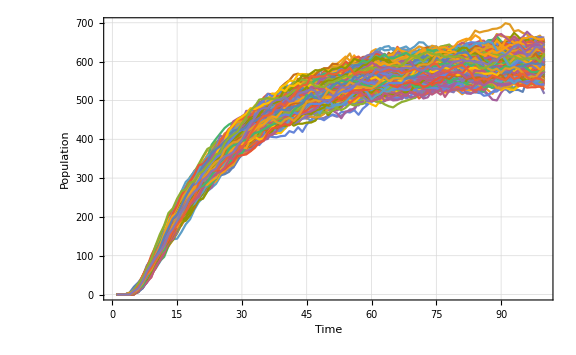

```mathematica
ListLinePlot[data,Frame->True,PlotTheme->"Detailed",FrameLabel->{"Time","Population"},ImageSize->Large]
```

```mathematica
Export[NotebookDirectory[]<>"InverseGammaXVar10.csv",Transpose@data];
```